```mathematica
NS["study_overlearningsimple_conj1"]
```

```mathematica
(* coords transfs to plot the two-distribution space *)
```

```mathematica
trmatrix=T[{{1,0},{1/2,Sqrt[3]/2}, {0,0}}];proj[p_]:=trmatrix.p;

plotfreqs[freqs_]:=Block[{nfreqs=(#/Total@#)&@Flatten@freqs},Graphics[{{PointSize@Large,red,Point[proj@nfreqs]}}]];
plotcfreqs[freqs_]:=Block[{nfreqs=(#/Total@#)&@Flatten@freqs},Graphics[{{Thick,red,Circle[proj@nfreqs,0.02]}}]];
sp1={Black,Thin,Line[T[trmatrix][[{1,2,3,1}]]]};
```

```mathematica
(* parametric model *)
ls=Range[0,2];g[s_]:=1+KroneckerDelta[s,1];SetAttributes[g,Listable];
expsum[t_]=Table[g[s]*Exp[t*s],{s,ls}];
z[t_]=Total@expsum[t];
prob[t_]=Simplify[expsum[t]/z[t]]
```

{1/((1+ⅇ^t)^2),(2 ⅇ^t)/((1+ⅇ^t)^2),ⅇ^(2 t)/((1+ⅇ^t)^2)}

```mathematica
Integrate[Evaluate[Times@@(prob[t]^{a,b,c})],{t,-Infinity,Infinity},Assumptions->(a>1&&b>1&&c>1&&Element[a,Integers]&&Element[b,Integers]&&Element[c,Integers])]
```

2^b (Hypergeometric2F1[2 a+b,2 (a+b+c),1+2 a+b,-1]/(2 a+b)+Hypergeometric2F1[2 (a+b+c),b+2 c,1+b+2 c,-1]/(b+2 c))

```mathematica
Assuming[(a>1&&b>1&&c>1&&Element[a,Integers]&&Element[b,Integers]&&Element[c,Integers]),FS@%]
```

(-2)^b (Beta[-1,2 a+b,1-2 (a+b+c)]+Beta[-1,b+2 c,1-2 (a+b+c)])

```mathematica
Integrate[Evaluate[Times@@(prob[t]^{a,b,c})],{t,-Infinity,Infinity},Assumptions->(a>0&&b>0&&c>0)]
```

2^b (Hypergeometric2F1[2 a+b,2 (a+b+c),1+2 a+b,-1]/(2 a+b)+Hypergeometric2F1[2 (a+b+c),b+2 c,1+b+2 c,-1]/(b+2 c))

```mathematica
Assuming[(a>0&&b>0&&c>0),FS@%]
```

2^b (Gamma[2 a+b] Hypergeometric2F1Regularized[2 a+b,2 (a+b+c),1+2 a+b,-1]+Gamma[b+2 c] Hypergeometric2F1Regularized[2 (a+b+c),b+2 c,1+b+2 c,-1])

```mathematica
uconj[t_,k_,n_]=Exp[k*t]/z[t]^n;
qq[k_,n_]=Assuming[0<k<2*n&&Element[k,Integers]&&Element[n,Integers],FullSimplify@Integrate[uconj[t,k,n],{t,-Infinity,Infinity}]]
```

(-1)^k (Beta[-1,k,1-2 n]+Beta[-1,-k+2 n,1-2 n])

```mathematica
conj[t_,k_,n_]=uconj[t,k,n]/qq[k,n]
```

((-1)^-k ⅇ^(k t) (1+2 ⅇ^t+ⅇ^(2 t))^-n)/(Beta[-1,k,1-2 n]+Beta[-1,-k+2 n,1-2 n])

```mathematica
cprob[s_,k_,n_]=Assuming[k>0&&n>k/2&&0<s<2,FS[g[s]*qq[k+s,n+1]/qq[k,n]]];
SetAttributes[cprob,Listable]
```

```mathematica
maxt[k_,n_]=(t/.Flatten@Assuming[k>0&&n>k/2,FS@Solve[D[uconj[t,k,n],t]==0,t,Reals]])
```

Log[-k/(k-2 n)]

```mathematica
mprob[k_,n_]=Assuming[k>0&&n>k/2,FS@prob[maxt[k,n]]]
```

{(k-2 n)^2/(4 n^2),-(k (k-2 n))/(2 n^2),k^2/(4 n^2)}

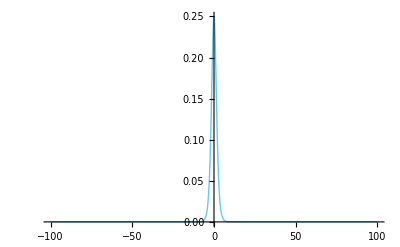

```mathematica
Plot[conj[t,1,1],{t,-100,100},PlotRange->{0,All}]
```

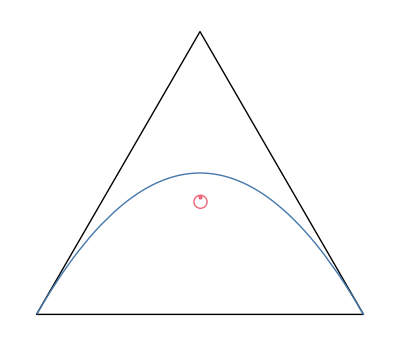

```mathematica
rfreqs=Flatten@{1/2*7/12,5/12,1/2*7/12};

samples=50;
data=RandomChoice[rfreqs->ls,samples];

rfreqs0=(#/Total@#)&@(Count[data+1,#]&/@{1,2,3});


ppplot1=ParametricPlot[proj@prob[t],{t,-100,100},Axes->None,PlotRange->All,AspectRatio->Auto,PlotStyle->{Thick,purpleblue}];
ddoms={Graphics[{sp1}],ppplot1};
Show[{ddoms,plotfreqs@rfreqs,plotcfreqs@rfreqs0},PlotRange->All]
```

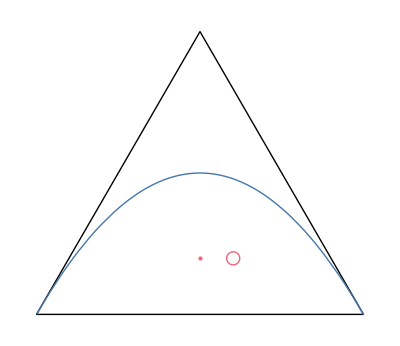

```mathematica
rfreqs={2/5,1/5,2/5};
data={0, 1, 1, 2, 0, 2, 0, 0, 0, 2};
samples=Length[data];
rfreqs0=(#/Total@#)&@(Count[data,#]&/@ls);


ppplot1=ParametricPlot[proj@prob[t],{t,-100,100},Axes->None,PlotRange->All,AspectRatio->Auto,PlotStyle->{Thick,purpleblue}];
ddoms={Graphics[{sp1}],ppplot1};
Show[{ddoms,plotfreqs@rfreqs,plotcfreqs@rfreqs0},PlotRange->All]
```

```mathematica
ProgressIndicator[Dynamic[i],{0,samples}]
```

```mathematica
samples=Length[data];
sdata=data+1;
kk0=1;nn0=1;qq0=qq[kk0,nn0];
gls=g[ls];
probh=Table[Null,{samples}];
mprobh=Table[Null,{samples}];
hitp=Table[Null,{samples}];
hitmp=Table[Null,{samples}];
logev=Table[Null,{samples}];
kkl=Table[Null,{samples}];
nnl=Table[Null,{samples}];

freqs=Table[0,{3}];oldqq=qq0;
Do[(*Print[i];Print[freqs];*)
kkl[[i]]=kk0+(ls.freqs);
nnl[[i]]=nn0+i-1;
newqq=(Times@@(gls^freqs))*gls*
qq[kkl[[i]]+ls,nnl[[i]]+1];
(*Print[{i,integral//MF}];*)

probh[[i]]=newqq/oldqq;
mprobh[[i]]=mprob[kkl[[i]],nnl[[i]]];
(*Print[integral];Print[probh[[i]]];Print[sdata[[i]]];*)
hitp[[i]]=probh[[i,sdata[[i]]]];
hitmp[[i]]=mprobh[[i,sdata[[i]]]];

oldqq=newqq[[sdata[[i]]]];
logev[[i]]=Log[oldqq/qq0];
++freqs[[sdata[[i]]]];
,{i,samples}]
```

```mathematica
T@Re@mprobh//N//MF
```

(0.25 | 0.5625 | 0.444444 | 0.390625 | 0.25 | 0.340278 | 0.25 | 0.316406 | 0.373457 | 0.4225
0.5 | 0.375 | 0.444444 | 0.46875 | 0.5 | 0.486111 | 0.5 | 0.492188 | 0.475309 | 0.455
0.25 | 0.0625 | 0.111111 | 0.140625 | 0.25 | 0.173611 | 0.25 | 0.191406 | 0.151235 | 0.1225)

```mathematica
Re@logev//N
```

{-1.09861,-2.30259,-3.26767,-5.05943,-6.35871,-8.00737,-9.32912,-10.4351,-11.3871,-13.402}

```mathematica
data
```

{0,1,1,2,0,2,0,0,0,2}

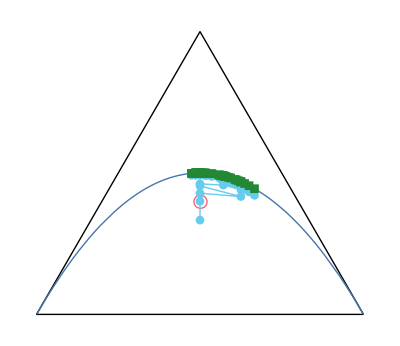

```mathematica
subrange=Round[Range[1,samples,samples/samples]];rplot1=ListPlot[T@Table[{proj@probh[[i]],proj@mprobh[[i]]},{i,subrange}],Axes->None,PlotRange->All,PlotStyle->{blue,green},Joined->True,PlotMarkers->Auto];
Show[{ddoms,plotfreqs@rfreqs,plotcfreqs@freqs,rplot1},PlotRange->All]
```

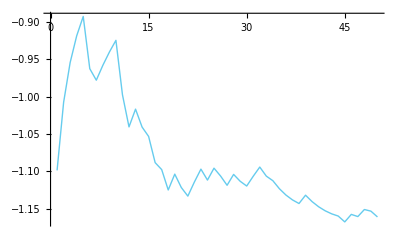

```mathematica
ListPlot[logev/Range[samples],Joined->True,PlotRange->All]
```

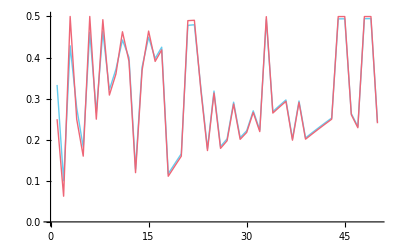

```mathematica
ListPlot[{hitp,hitmp},Joined->True,PlotRange->All]
```

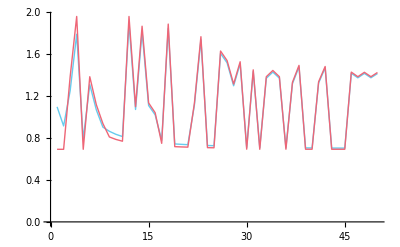

```mathematica
ListPlot[-Log[{hitp,hitmp}],Joined->True,PlotRange->All]
```

```mathematica
entropy[p_]:=Block[{xlogx},
xlogx[x_]:=If[x>0,x*Log[x],0];
SetAttributes[xlogx,Listable];
Total@xlogx[p]];
```

```mathematica
(Exp@-entropy[rfreqs])^10*2//N
```

100218.

```mathematica
Log[Exp@-entropy[rfreqs],100000]//N
```

10.6385

```mathematica
rfreqs
```

{3/8,3/8,1/4}

```mathematica
(* cut *)
```

```mathematica
priort[t_,m_,s_]:=(PDF[NormalDistribution[m,s],t]+PDF[NormalDistribution[-m,s],t])/2;
```

```mathematica
priort[t_,m_,s_]:=(PDF[NormalDistribution[m,s],t]);
```

```mathematica
(* representation of parameter density on simplex *)
```

```mathematica
tran[t_]=FS[prob[t][[3]]]
```

1/(1+(2 Cosh[t])/11)

```mathematica
somax=prob[0][[3]]
```

11/13

```mathematica
dpdt[t_]=Assuming[Element[t,Reals],FullSimplify[Abs@D[tran[t],t]]]
```

(22 Abs[Sinh[t]])/(11+2 Cosh[t])^2

```mathematica
inve[so_]=t/.Flatten[Assuming[0<so<somax,FS@Solve[so==tran[t],t,Reals]]]
```

-ArcCosh[-(11 (-1+so))/(2 so)]

```mathematica
Plot[inve[so],{so,0,somax}]
```

```mathematica
dens[so_,mx_,sx_]=2*Assuming[0<so<somax,Simplify@priort[inve[so],mx,sx]/dpdt[inve[so]]]
```

((ⅇ^(-(mx-ArcCosh[-(11 (-1+so))/(2 so)])^2/(2 sx^2))+ⅇ^(-(mx+ArcCosh[-(11 (-1+so))/(2 so)])^2/(2 sx^2))) (11-(11 (-1+so))/so)^2)/(22 √(2 π) sx Abs[√((-1-(11 (-1+so))/(2 so))/(1-(11 (-1+so))/(2 so))) (1-(11 (-1+so))/(2 so))])

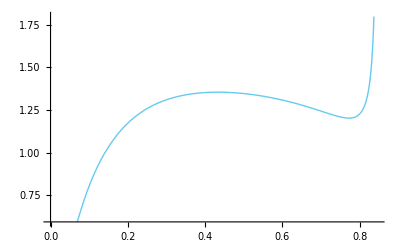

```mathematica
Plot[dens[so,2.5,1.2],{so,0,somax},PlotRange->Auto]
```

```mathematica
Limit[dens[so,6,1/2],so->somax]
```

∞

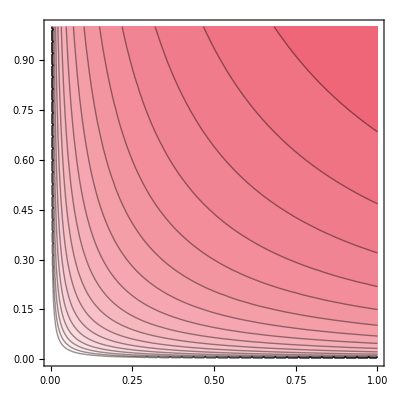

```mathematica
ContourPlot[Log[x*y],{x,0,1},{y,0,1},ColorFunction->mycolorfunction,Contours->20]
```